```mathematica
(*Solving hamilton's equation of SHO*)
(*first of all define the hamiltonian of SHO*)
H[p_,q_]:=p^2/(2 m)+m w^2q^2/2;
(*p is the momentum ad q is the displacement*)
(*get the expression of hamilonian*)
Hamiltonian=H[p[t],q[t]]
```

p[t]^2/(2 m)+1/2 m w^2 q[t]^2

```mathematica
(*defne the hmilton equations*)
Heq1=p'[t]==-D[Hamiltonian,q[t]]
Heq2=q'[t]==D[Hamiltonian,p[t]]
```

p'[t]==-m w^2 q[t]

q'[t]==p[t]/m

```mathematica
sol=DSolve[{Heq1,Heq2},{p[t],q[t]},t]
```

{{p[t]→C[1] Cos[t w]-m w C[2] Sin[t w],q[t]→C[2] Cos[t w]+(C[1] Sin[t w])/(m w)}}

```mathematica
momentum=p[t]/.sol[[1]]
displ=q[t]/.sol[[1]]
```

C[1] Cos[t w]-m w C[2] Sin[t w]

C[2] Cos[t w]+(C[1] Sin[t w])/(m w)

```mathematica
eq1=(momentum/.t->0)==0
eq2=(displ/.t->0)==5
```

C[1]==0

C[2]==5

```mathematica
const=Solve[{eq1,eq2},{C[1],C[2]}]
```

{{C[1]→0,C[2]→5}}

```mathematica
p=momentum/.const[[1]]/.{m->2,w->1}
x=displ/.const[[1]]/.{m->2,w->1}
```

-10 Sin[t]

5 Cos[t]

```mathematica
force=D[p,t]
```

-10 Cos[t]

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i.

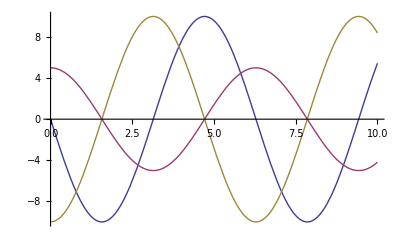

```mathematica
Plot[{p,x,force},{t,0,10}]
```

```mathematica
?ParametricPlot
```

ParametricPlot[{f_x,f_y},{u,u_min,u_max}] generates a parametric plot of a curve with x and y coordinates f_x and f_y as a function of u. 
ParametricPlot[{{f_x,f_y},{g_x,g_y},…},{u,u_min,u_max}] plots several parametric curves. 
ParametricPlot[{f_x,f_y},{u,u_min,u_max},{v,v_min,v_max}] plots a parametric region. 
ParametricPlot[{{f_x,f_y},{g_x,g_y},…},{u,u_min,u_max},{v,v_min,v_max}] plots several parametric regions.

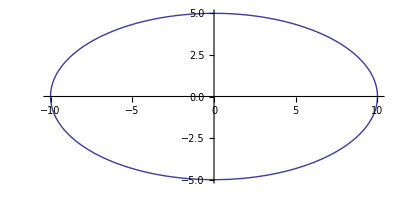

```mathematica
ParametricPlot[{p,x},{t,0,2*Pi}]
```